```mathematica
pointfile = FileNameJoin[{NotebookDirectory[], "points.txt"}]
```

D:\Desktop\ChargeDistribution\points.txt

```mathematica
ListPointPlot3D[ToExpression[Import[pointfile]],Boxed->True,Axes->True, BoxRatios->Automatic]
```

```mathematica
x=R*Cos[t]
```

R Cos[t]

```mathematica
y=R*Sin[t]
```

R Sin[t]

```mathematica
r1=(x-R/4)^2+y^2
```

(-R/4+R Cos[t])^2+R^2 Sin[t]^2

```mathematica
1/r1
```

1/((-R/4+R Cos[t])^2+R^2 Sin[t]^2)

```mathematica
Simplify[1/((-R/4+R Cos[t])^2+R^2 Sin[t]^2)]
```

16/(R^2 (17-8 Cos[t]))

```mathematica
E^(I Pi)
```

-1

```mathematica
SphericalPlot3D[0.02(2+1/10 theta^3 Sin[3phi] Sin[6theta]),{theta,0,π},{phi,0,2 π}]
```

-Graphics3D-

```mathematica
normvec = "D:/Desktop/ChargeDistribution/normvec.txt"
```

D:/Desktop/ChargeDistribution/normvec.txt

```mathematica
ToExpression[Import[normvec]]
```

{{-0.075,-0.075,-0.075},{0.494233,0.0349936,0.868625},{-0.075,-0.075,-0.065},{0.494233,0.0349936,0.868625},8184,{0.075,0.075,0.065},{-0.40999,0.035509,-0.911399},{0.075,0.075,0.075},{-0.40999,0.035509,-0.911399}}
 |  |  |  |

```mathematica
ListVectorPlot3D[ToExpression[Import[normvec]]]
```

Visualization`Core`ListVectorPlot3D::vfldata: {{-0.075,-0.075,-0.075},{0.494233,0.0349936,0.868625},{-0.075,-0.075,-0.065},{0.494233,0.0349936,0.868625},{-0.075,-0.075,-0.055},«42»,{0.494233,0.0349936,0.868625},{-0.075,-0.065,0.005},{0.494233,0.0349936,0.868625},«8142»} is not a valid vector field dataset or a valid list of datasets.

ListVectorPlot3D[{{-0.075,-0.075,-0.075},{0.494233,0.0349936,0.868625},{-0.075,-0.075,-0.065},{0.494233,0.0349936,0.868625},8185,{-0.40999,0.035509,-0.911399},{0.075,0.075,0.075},{-0.40999,0.035509,-0.911399}}]
 |  |  |  |

```mathematica
theta := u 2Pi;
z:=0.12 v - 0.06;
c:=1/Sqrt[3]0.06;
x:=0.04/2 Sqrt[1+z^2/c^2] Cos[theta];
y:=0.04/2Sqrt[1+z^2/c^2] Sin[theta]
ParametricPlot3D[{(x+128 z^3),(y+20x^2+10z^2),z},{u,0,1},{v,0,1}]
```

-Graphics3D-

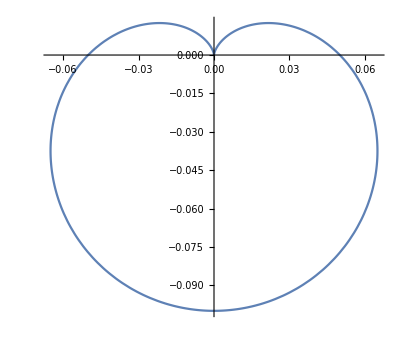

```mathematica
x:=a*(1-Sin[t])*Cos[t];
y:=a*(1-Sin[t])*Sin[t];
ParametricPlot[{x,y}/.a->0.05,{t,0,2Pi}]
```

```mathematica
x1:=D[x,t];
x2 :=D[x,{t,2}];
y1:=D[y,t];
y2 :=D[y,{t,2}];
```

```mathematica
e=FullSimplify[(x1^2-y1^2)*(x1^3*y2+x2*y1^3)/(x1^2+y1^2)^2]
```

1/2 a^2 (-1+Sin[t]) (1-2 Cos[2 t]+2 Sin[t]-7 Sin[3 t]) Sin[3 t]

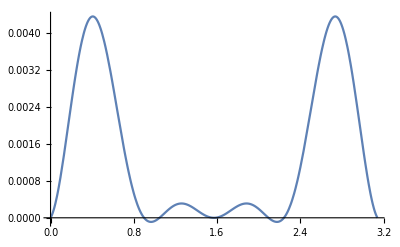

```mathematica
Plot[e/.a->0.05,  {t,0,Pi}]
```